## VerticesOnBoundary-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51i (18 June 2017)) loaded Sun 18 Jun 2017 18:00:26
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

There are 8 cells in the tissue.

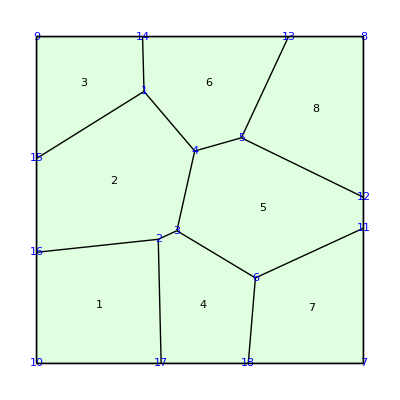

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True, "VertexNumbers"-> {Blue,FontSize-> 18}]
```

```mathematica
VerticesOnBoundary[q]
```

{7,11,12,8,13,14,9,15,16,10,17,18}

```mathematica
VerticesNotOnBoundary[q]
```

{1,2,3,4,5,6}